{{a[n]→1/2 (2+n+n^2)}}

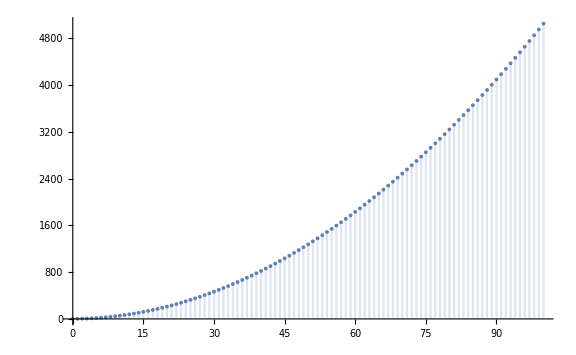

Result {lines, regions}: 
{{0,1},{5,16},{10,56},{15,121},{20,211},{25,326},{30,466},{35,631},{40,821},{45,1036},{50,1276},{55,1541},{60,1831},{65,2146},{70,2486},{75,2851},{80,3241},{85,3656},{90,4096},{95,4561},{100,5051}}

```mathematica
(*Clear everything*)
Clear["`*"];
(*Initial condition: 0 line, 1 plane; 1 line, 2 half-planes (regions) *)
iv1=a[0]==1;
iv2=a[1]==2;
(*Since there is no parallel nor *** line, one new line will cross n lines, cross n regions plus the final empty halfplane, divides it into 2 halfplanes *)
rr=a[n+1]==a[n]+n+1;
(*Solve it by Mathematica *)
sol=RSolve[{rr,iv1,iv2},a[n],n] // Simplify
a[n_]=a[n]/.sol[[1]];
DiscretePlot[Evaluate[a[n]]/.sol[[1]],{n,0,100}]
(*Exporting and ploting*)

data = Table[{n,a[n]},{n,0,100,5}];
Print["Result {lines, regions}: \n",data];
```